```mathematica
2-2
```

0

REMARK: Go to the Evaluation menu and click on Evaluate Notebook.  To launch the animations that appear at the end of the notebook, move the top slider to mid position of higher, punch the + tab on the right end of the lower slide and hit the start button (▲).

# Classical Ozone

## An illustration of how one identifies the vibrational modes of "classical molecules"

Nicholas Wheeler
Reed College Physics 
20 October 2007

Three particles of identical mass  m  are connected, each to the other two, by identical springs of strength k. The system—if imagined to be confined to a plane—has 6 degrees of freedom. We expect it therefore to possess 6 normal modes. Our assignment is to describe them. The following diagram sets our notation:

```mathematica
α=Sin[π/6];
β=Sin[π/3];
```

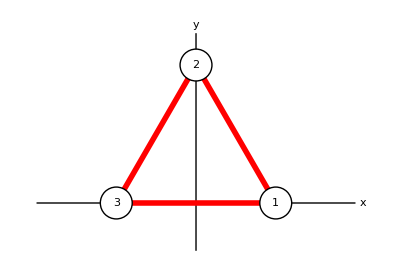

```mathematica
Graphics[{Line[{{-1,0},{1,0}}],
Line[{{0,-0.3},{0,β+.2}}],
{Red,Thickness[.01],Line[{{-α,0},{α,0}}]},
{Red,Thickness[.01],Line[{{α,0},{0,β}}]},
{Red,Thickness[.01],Line[{{-α,0},{0,β}}]},
{White,Disk[{α,0},.1]},
{White,Disk[{-α,0},.1]},
{White,Disk[{0,β},.1]},
Circle[{α,0},.1],
Circle[{-α,0},.1],
Circle[{0,β},.1],
Text[1,{α,0}],
Text[2,{0,β}],
Text[3,{-α,0}],
Text[x,{1.05,0}],
Text[y,{0,β+.25}]}]
```

Our first assignment is to describe the energy invested in the spring system when the particles are subjected to small displacements from their equilibrium positions. That is easy if we know how to describe how much a spring is stretched when its endpoints are displaced. Let vectors

(a1
b1) and (a2
b2)

mark the endpoints of a spring. Then

```mathematica
SpringLength[({{a1_}, {b1_}}),({{a2_}, {b2_}})]:=√((a1-a2)^2+(b1-b2)^2)
```

Proceeding in reference to the figure, we find that the lengths of the springs 1↔2, 2↔3 and 3↔1 are given respectively by

```mathematica
SpringLength[({{α}, {0}}),({{0}, {β}})]
SpringLength[({{0}, {β}}),({{-α}, {0}})]
SpringLength[({{-α}, {0}}),({{α}, {0}})]
```

1

1

1

Which is to say: all have unit length when unstretched. Now let

ϵ(x1
y1), ϵ(x2
y2)   and   ϵ(x3
y3)

describe small displacements of the particles from their equilibrium positions.  Then

```mathematica
Series[SpringLength[({{α+ϵ x1}, {ϵ y1}}),({{ϵ x2}, {β+ϵ y2}})]-1,{ϵ,0,1}]//Normal
Series[SpringLength[({{ϵ x2}, {β+ϵ y2}}),({{-α+ϵ x3}, {ϵ y3}})]-1,{ϵ,0,1}]//Normal
Series[SpringLength[({{-α+ϵ x3}, {ϵ y3}}),({{α+ϵ x1}, {ϵ y1}})]-1,{ϵ,0,1}]//Normal
```

1/2 (x1-x2-√3 y1+√3 y2) ϵ

1/2 (x2-x3+√3 y2-√3 y3) ϵ

(x1-x3) ϵ

provide leading-order descriptions of how much the springs are stretched as a result of those displacements.

The potential energy of the spring system has become

U=1/2 k S

where

```mathematica
S=(1/2 (x1-x2-√3 y1+√3 y2))^2+(1/2 (x2-x3+√3 y2-√3 y3))^2+(x1-x3)^2//Expand
```

(5 x1^2)/4-(x1 x2)/2+x2^2/2-2 x1 x3-(x2 x3)/2+(5 x3^2)/4-1/2 √3 x1 y1+1/2 √3 x2 y1+(3 y1^2)/4+1/2 √3 x1 y2-1/2 √3 x3 y2-(3 y1 y2)/2+(3 y2^2)/2-1/2 √3 x2 y3+1/2 √3 x3 y3-(3 y2 y3)/2+(3 y3^2)/4

This is a quadratic form in 6 variables, so can be written as a 6-vector wrapped around a symmetric 6×6 matrix. By inspection we are led to write

```mathematica
S==(Transpose[({{x1}, {y1}, {x2}, {y2}, {x3}, {y3}})].({{5/4, -(√3)/4, -1/4, (√3)/4, -1, 0}, {-(√3)/4, 3/4, (√3)/4, -3/4, 0, 0}, {-1/4, (√3)/4, 1/2, 0, -1/4, -(√3)/4}, {(√3)/4, -3/4, 0, 3/2, -(√3)/4, -3/4}, {-1, 0, -1/4, -(√3)/4, 5/4, (√3)/4}, {0, 0, -(√3)/4, -3/4, (√3)/4, 3/4}}).({{x1}, {y1}, {x2}, {y2}, {x3}, {y3}}))⟦1⟧⟦1⟧//Expand
```

True

Look to the spectrum of

```mathematica
𝕂=({{5/4, -(√3)/4, -1/4, (√3)/4, -1, 0}, {-(√3)/4, 3/4, (√3)/4, -3/4, 0, 0}, {-1/4, (√3)/4, 1/2, 0, -1/4, -(√3)/4}, {(√3)/4, -3/4, 0, 3/2, -(√3)/4, -3/4}, {-1, 0, -1/4, -(√3)/4, 5/4, (√3)/4}, {0, 0, -(√3)/4, -3/4, (√3)/4, 3/4}});
```

```mathematica
Spectrum=Reverse[Eigenvalues[𝕂]]
```

{0,0,0,3/2,3/2,3}

and give those eigenvalues names:

```mathematica
{Subscript[λ, 0], Subscript[λ, 0],Subscript[λ, 0],Subscript[λ, 1], Subscript[λ, 1],Subscript[λ, 2]}=Spectrum;
```

It is now evident that 𝕂 has a 3-dimensional null space. Mathematica supplies null vectors

```mathematica
NullSpace[({{5/4, -(√3)/4, -1/4, (√3)/4, -1, 0}, {-(√3)/4, 3/4, (√3)/4, -3/4, 0, 0}, {-1/4, (√3)/4, 1/2, 0, -1/4, -(√3)/4}, {(√3)/4, -3/4, 0, 3/2, -(√3)/4, -3/4}, {-1, 0, -1/4, -(√3)/4, 5/4, (√3)/4}, {0, 0, -(√3)/4, -3/4, (√3)/4, 3/4}})]
```

{{0,-1,√3,0,0,1},{1,0,1,0,1,0},{0,2,-√3,1,0,0}}

which are, as it happens, not orthogonal:

```mathematica
{0,-1,√3,0,0,1}.{1,0,1,0,1,0}
{0,-1,√3,0,0,1}.{0,2,-√3,1,0,0}
{1,0,1,0,1,0}.{0,2,-√3,1,0,0}
```

√3

-5

-√3

We notice, however, that

```mathematica
{0,-1,√3,0,0,1}+{0,2,-√3,1,0,0}
```

{0,1,0,1,0,1}

is clearly orthogonal  to {1, 0, 1, 0, 1, 0}. We are led thus to define orthonormal null vectors

```mathematica
Subscript[N, 1]=({{1/(√3)}, {0}, {1/(√3)}, {0}, {1/(√3)}, {0}});
Subscript[N, 2]=({{0}, {1/(√3)}, {0}, {1/(√3)}, {0}, {1/(√3)}});
```

To complete the construction of an orthonormal basis in the null space of 𝕂 we subtract the N_1 and N_2 components of {0,-1,√3,0,0,1}, which is to say: we define

```mathematica
u={0,-1,√3,0,0,1};
Subscript[n, 1]={1/(√3), 0, 1/(√3), 0, 1/(√3), 0};
Subscript[n, 2]={0, 1/(√3), 0, 1/(√3), 0, 1/(√3)};
```

construct

```mathematica
u-Subscript[n, 1](Subscript[n, 1].u)-Subscript[n, 2](Subscript[n, 2].u)
```

{-1/(√3),-1,-1/(√3)+√3,0,-1/(√3),1}

```mathematica
%/(√(%.%))//Simplify
```

{-1/(2 √3),-1/2,1/(√3),0,-1/(2 √3),1/2}

and so (by what has been simply the standard Gram-Schmidt orthogonalization procedure) are led to the unit null vector

```mathematica
Subscript[N, 3]=({{-1/(2 √3)}, {-1/2}, {1/(√3)}, {0}, {-1/(2 √3)}, {1/2}});
```

Looking now to the non-null eigevectors, we construct

```mathematica
EigenvectorList=Reverse[Eigenvectors[({{5/4, -(√3)/4, -1/4, (√3)/4, -1, 0}, {-(√3)/4, 3/4, (√3)/4, -3/4, 0, 0}, {-1/4, (√3)/4, 1/2, 0, -1/4, -(√3)/4}, {(√3)/4, -3/4, 0, 3/2, -(√3)/4, -3/4}, {-1, 0, -1/4, -(√3)/4, 5/4, (√3)/4}, {0, 0, -(√3)/4, -3/4, (√3)/4, 3/4}})]]
```

{{0,2,-√3,1,0,0},{1,0,1,0,1,0},{0,-1,√3,0,0,1},{-1/2,-(√3)/2,-1/2,(√3)/2,1,0},{(√3)/2,-1/2,-(√3)/2,-1/2,0,1},{-√3,1,0,-2,√3,1}}

and strike the first three vectors (those are the null vectors, already discussed). We are left with

```mathematica
Subscript[a, 1]=Transpose[{EigenvectorList⟦4⟧}];
Subscript[a, 2]=Transpose[{EigenvectorList⟦5⟧}];
b=Transpose[{EigenvectorList⟦6⟧}];
```

Those we normalize, producing

```mathematica
Subscript[A, 1]=Subscript[a, 1]/(√(Flatten[Transpose[Subscript[a, 1]].Subscript[a, 1]]⟦1⟧));
Subscript[A, 2]=Subscript[a, 2]/(√(Flatten[Transpose[Subscript[a, 2]].Subscript[a, 2]]⟦1⟧));
B=b/(√(Flatten[Transpose[b].b]⟦1⟧));
```

We pause to demonstrate that the 6 vectors now in our possession are in fact orthonormal:

```mathematica
DotProd[X_,Y_]:=Flatten[X].Flatten[Y]
```

```mathematica
{{DotProd[Subscript[N, 1],Subscript[N, 1]], DotProd[Subscript[N, 1],Subscript[N, 2]], DotProd[Subscript[N, 1],Subscript[N, 3]], DotProd[Subscript[N, 1],Subscript[A, 1]], DotProd[Subscript[N, 1],Subscript[A, 2]], DotProd[Subscript[N, 1],B]}, {□, DotProd[Subscript[N, 2],Subscript[N, 2]], DotProd[Subscript[N, 2],Subscript[N, 3]], DotProd[Subscript[N, 2],Subscript[A, 1]], DotProd[Subscript[N, 2],Subscript[A, 2]], DotProd[Subscript[N, 2],B]}, {□, □, DotProd[Subscript[N, 3],Subscript[N, 3]], DotProd[Subscript[N, 3],Subscript[A, 1]], DotProd[Subscript[N, 3],Subscript[A, 2]], DotProd[Subscript[N, 3],B]}, {□, □, □, DotProd[Subscript[A, 1],Subscript[A, 1]], DotProd[Subscript[A, 1],Subscript[A, 2]], DotProd[Subscript[A, 1],B]}, {□, □, □, □, DotProd[Subscript[A, 2],Subscript[A, 2]], DotProd[Subscript[A, 2],B]}, {□, □, □, □, □, DotProd[B,B]}}//TableForm
```

1 | 0 | 0 | 0 | 0 | 0
□ | 1 | 0 | 0 | 0 | 0
□ | □ | 1 | 0 | 0 | 0
□ | □ | □ | 1 | 0 | 0
□ | □ | □ | □ | 1 | 0
□ | □ | □ | □ | □ | 1

and that they are in fact eigenvectors of 𝕂:

```mathematica
ZeroVector=({{0}, {0}, {0}, {0}, {0}, {0}});
```

```mathematica
𝕂.Subscript[N, 1]==ZeroVector
𝕂.Subscript[N, 2]==ZeroVector
𝕂.Subscript[N, 3]==ZeroVector

𝕂.Subscript[A, 1]==Subscript[λ, 1] Subscript[A, 1]
𝕂.Subscript[A, 2]==Subscript[λ, 1] Subscript[A, 2]

𝕂.B==Subscript[λ, 2] B
```

True

True

True

«3 more identical outputs»

### We look now to the molecular modes of which the preceding results speak:

```mathematica
({{x1}, {y1}, {x2}, {y2}, {x3}, {y3}})=Subscript[N, 1]
Subscript[ω, 0]=√Subscript[λ, 0]
```

{{1/(√3)},{0},{1/(√3)},{0},{1/(√3)},{0}}

0

REMARK: From

x''+ω^2 x==0

we see that "oscillation at zero frequency" is uniform rectilinear motion.

```mathematica
Manipulate[Graphics[{Line[{{-1,0},{1,0}}],
Line[{{0,-0.3},{0,β+.2}}],
{Red,Thickness[.01],Line[{{-α,0},{α,0}}]},
{Red,Thickness[.01],Line[{{α,0},{0,β}}]},
{Red,Thickness[.01],Line[{{-α,0},{0,β}}]},
{White,Disk[{α,0},.1]},
{White,Disk[{-α,0},.1]},
{White,Disk[{0,β},.1]},
Circle[{α,0},.1],
Circle[{-α,0},.1],
Circle[{0,β},.1],
Text[x,{1.05,0}],
Text[y,{0,β+.25}],
{Red,Disk[{α+x1 v t,0+y1 v  t},.08]},
{Red,Disk[{0+x2 v  t,β+y2 v t},.08]},
{Red,Disk[{-α+x3 v  t,0+y3 v  t},.08]}},PlotRange->{-0.4,β+.3},PlotLabel->Style["x-Translation at Zero Frequency",
 FontFamily->"Helvetica", FontSize->14]],{v,0,3},{t,0,α/2}]
```

```mathematica
({{xa1}, {ya1}, {xa2}, {ya2}, {xa3}, {ya3}})=Subscript[N, 2]
Subscript[ω, 0]=√Subscript[λ, 0]
```

{{0},{1/(√3)},{0},{1/(√3)},{0},{1/(√3)}}

0

```mathematica
Manipulate[Graphics[{Line[{{-1,0},{1,0}}],
Line[{{0,-0.3},{0,β+.2}}],
{Red,Thickness[.01],Line[{{-α,0},{α,0}}]},
{Red,Thickness[.01],Line[{{α,0},{0,β}}]},
{Red,Thickness[.01],Line[{{-α,0},{0,β}}]},
{White,Disk[{α,0},.1]},
{White,Disk[{-α,0},.1]},
{White,Disk[{0,β},.1]},
Circle[{α,0},.1],
Circle[{-α,0},.1],
Circle[{0,β},.1],
Text[x,{1.05,0}],
Text[y,{0,β+.25}],
{Red,Disk[{α+xa1 v  t,0+ya1 v   t},.08]},
{Red,Disk[{0+xa2  v  t,β+ya2 v   t},.08]},
{Red,Disk[{-α+xa3 v   t,0+ya3 v   t},.08]}},PlotRange->{-0.4,β+.3},PlotLabel->Style["y-Translation at Zero Frequency",
 FontFamily->"Helvetica", FontSize->14]],{v,0,3},{t,0,α/2}]
```

```mathematica
({{xb1}, {yb1}, {xb2}, {yb2}, {xb3}, {yb3}})=Subscript[N, 3]//Simplify
Subscript[ω, 0]=√Subscript[λ, 0]
```

{{-1/(2 √3)},{-1/2},{1/(√3)},{0},{-1/(2 √3)},{1/2}}

0

```mathematica
Manipulate[Graphics[{Line[{{-1,0},{1,0}}],
Line[{{0,-0.3},{0,β+.2}}],
{Red,Thickness[.01],Line[{{-α,0},{α,0}}]},
{Red,Thickness[.01],Line[{{α,0},{0,β}}]},
{Red,Thickness[.01],Line[{{-α,0},{0,β}}]},
{White,Disk[{α,0},.1]},
{White,Disk[{-α,0},.1]},
{White,Disk[{0,β},.1]},
Circle[{α,0},.1],
Circle[{-α,0},.1],
Circle[{0,β},.1],
Text[x,{1.05,0}],
Text[y,{0,β+.25}],
{Red,Disk[{α+xb1 t,0+yb1 t},.08]},
{Red,Disk[{0+xb2 t,β+yb2 t},.08]},
{Red,Disk[{-α+xb3 t,0+yb3 t},.08]}},PlotRange->{-0.4,β+.3},PlotRange->{-0.4,β+.3},PlotLabel->Style["Rotation at Zero Frequency",
 FontFamily->"Helvetica", FontSize->14]],{t,0,α/2}]
```

```mathematica
({{xc1}, {yc1}, {xc2}, {yc2}, {xc3}, {yc3}})=Subscript[A, 1]
Subscript[ω, 1]=√Subscript[λ, 1]
```

{{-1/(2 √3)},{-1/2},{-1/(2 √3)},{1/2},{1/(√3)},{0}}

√(3/2)

```mathematica
Manipulate[Graphics[{Line[{{-1,0},{1,0}}],
Line[{{0,-0.3},{0,β+.2}}],
{Red,Thickness[.01],Line[{{-α,0},{α,0}}]},
{Red,Thickness[.01],Line[{{α,0},{0,β}}]},
{Red,Thickness[.01],Line[{{-α,0},{0,β}}]},
{White,Disk[{α,0},.1]},
{White,Disk[{-α,0},.1]},
{White,Disk[{0,β},.1]},
Circle[{α,0},.1],
Circle[{-α,0},.1],
Circle[{0,β},.1],
Text[x,{1.05,0}],
Text[y,{0,β+.25}],
{Red,Disk[{α+xc1 ϵ Sin[Subscript[ω, 1] t],0+yc1 ϵ Sin[Subscript[ω, 1] t]},.08]},
{Red,Disk[{0+xc2 ϵ Sin[Subscript[ω, 1] t],β+yc2 ϵ Sin[Subscript[ω, 1] t]},.08]},
{Red,Disk[{-α+xc3 ϵ Sin[Subscript[ω, 1] t],0+yc3 ϵ Sin[Subscript[ω, 1] t]},.08]}},PlotRange->{-0.4,β+.3},PlotRange->{-0.4,β+.3},PlotLabel->Style["Strange Mode (Slow)",
 FontFamily->"Helvetica", FontSize->14]],{ϵ,0,0.5},{t,0,(2π)/Subscript[ω, 1]}]
```

```mathematica
({{xd1}, {yd1}, {xd2}, {yd2}, {xd3}, {yd3}})=Subscript[A, 2]
Subscript[ω, 1]=√Subscript[λ, 1]
```

{{1/2},{-1/(2 √3)},{-1/2},{-1/(2 √3)},{0},{1/(√3)}}

√(3/2)

```mathematica
Manipulate[Graphics[{Line[{{-1,0},{1,0}}],
Line[{{0,-0.3},{0,β+.2}}],
{Red,Thickness[.01],Line[{{-α,0},{α,0}}]},
{Red,Thickness[.01],Line[{{α,0},{0,β}}]},
{Red,Thickness[.01],Line[{{-α,0},{0,β}}]},
{White,Disk[{α,0},.1]},
{White,Disk[{-α,0},.1]},
{White,Disk[{0,β},.1]},
Circle[{α,0},.1],
Circle[{-α,0},.1],
Circle[{0,β},.1],
Text[x,{1.05,0}],
Text[y,{0,β+.25}],
{Red,Disk[{α+xd1 ϵ Sin[Subscript[ω, 1] t],0+yd1 ϵ Sin[Subscript[ω, 1] t]},.08]},
{Red,Disk[{0+xd2 ϵ Sin[Subscript[ω, 1] t],β+yd2 ϵ Sin[Subscript[ω, 1] t]},.08]},
{Red,Disk[{-α+xd3 ϵ Sin[Subscript[ω, 1] t],0+yd3 ϵ Sin[Subscript[ω, 1] t]},.08]}},PlotRange->{-0.4,β+.3},PlotLabel->Style["Flexing, with #1 Moving Radially (Slow)",
 FontFamily->"Helvetica", FontSize->14]],{ϵ,0,0.5},{t,0,(2π)/Subscript[ω, 1]}]
```

```mathematica
({{xe1}, {ye1}, {xe2}, {ye2}, {xe3}, {ye3}})=(Subscript[A, 2]-√3 Subscript[A, 1])/2//Simplify
```

{{1/2},{1/(2 √3)},{0},{-1/(√3)},{-1/2},{1/(2 √3)}}

```mathematica
Manipulate[Graphics[{Line[{{-1,0},{1,0}}],
Line[{{0,-0.3},{0,β+.2}}],
{Red,Thickness[.01],Line[{{-α,0},{α,0}}]},
{Red,Thickness[.01],Line[{{α,0},{0,β}}]},
{Red,Thickness[.01],Line[{{-α,0},{0,β}}]},
{White,Disk[{α,0},.1]},
{White,Disk[{-α,0},.1]},
{White,Disk[{0,β},.1]},
Circle[{α,0},.1],
Circle[{-α,0},.1],
Circle[{0,β},.1],
Text[x,{1.05,0}],
Text[y,{0,β+.25}],
{Red,Disk[{α+xe1 ϵ Sin[Subscript[ω, 1] t],0+ye1 ϵ Sin[Subscript[ω, 1] t]},.08]},
{Red,Disk[{0+xe2 ϵ Sin[Subscript[ω, 1] t],β+ye2 ϵ Sin[Subscript[ω, 1] t]},.08]},
{Red,Disk[{-α+xe3 ϵ Sin[Subscript[ω, 1] t],0+ye3 ϵ Sin[Subscript[ω, 1] t]},.08]}},PlotRange->{-0.4,β+.3},PlotLabel->Style["Composite Mode: Flexing, with #2 Moving Radially",
 FontFamily->"Helvetica", FontSize->14]],{ϵ,0,0.5},{t,0,(2π)/Subscript[ω, 1]}]
```

```mathematica
({{xf1}, {yf1}, {xf2}, {yf2}, {xf3}, {yf3}})=(Subscript[A, 2]+√3 Subscript[A, 1])/2//Simplify
```

{{0},{-1/(√3)},{-1/2},{1/(2 √3)},{1/2},{1/(2 √3)}}

```mathematica
Manipulate[Graphics[{Line[{{-1,0},{1,0}}],
Line[{{0,-0.3},{0,β+.2}}],
{Red,Thickness[.01],Line[{{-α,0},{α,0}}]},
{Red,Thickness[.01],Line[{{α,0},{0,β}}]},
{Red,Thickness[.01],Line[{{-α,0},{0,β}}]},
{White,Disk[{α,0},.1]},
{White,Disk[{-α,0},.1]},
{White,Disk[{0,β},.1]},
Circle[{α,0},.1],
Circle[{-α,0},.1],
Circle[{0,β},.1],
Text[x,{1.05,0}],
Text[y,{0,β+.25}],
{Red,Disk[{α+xf1 ϵ Sin[Subscript[ω, 1] t],0+yf1 ϵ Sin[Subscript[ω, 1] t]},.08]},
{Red,Disk[{0+xf2 ϵ Sin[Subscript[ω, 1] t],β+yf2 ϵ Sin[Subscript[ω, 1] t]},.08]},
{Red,Disk[{-α+xf3 ϵ Sin[Subscript[ω, 1] t],0+yf3 ϵ Sin[Subscript[ω, 1] t]},.08]}},PlotRange->{-0.4,β+.3},PlotLabel->Style["Composite Mode: Flexing, with #3 Moving Radially",
 FontFamily->"Helvetica", FontSize->14]],{ϵ,0,0.5},{t,0,(2π)/Subscript[ω, 1]}]
```

REMARK: The 6-vectors that give rise to flex modes

```mathematica
Subscript[f, 1]={{1/2},{-1/(2 √3)},{-1/2},{-1/(2 √3)},{0},{1/(√3)}};
Subscript[f, 2]={{1/2},{1/(2 √3)},{0},{-1/(√3)},{-1/2},{1/(2 √3)}};
Subscript[f, 3]={{0},{-1/(√3)},{-1/2},{1/(2 √3)},{1/2},{1/(2 √3)}};
```

are seen to be (apart from some signs that are easily seen to be irrelevant) cyclic permutations of one another. And they are linearly interdependent (collectively span a 2-dimensional subspace of 6-space).

```mathematica
Subscript[f, 1]==Subscript[f, 2]+Subscript[f, 3]
```

True

```mathematica
({{xg1}, {yg1}, {xg2}, {yg2}, {xg3}, {yg3}})=B
Subscript[ω, 2]=√Subscript[λ, 2]
```

{{-1/2},{1/(2 √3)},{0},{-1/(√3)},{1/2},{1/(2 √3)}}

√3

```mathematica
Manipulate[Graphics[{Line[{{-1,0},{1,0}}],
Line[{{0,-0.3},{0,β+.2}}],
{Red,Thickness[.01],Line[{{-α,0},{α,0}}]},
{Red,Thickness[.01],Line[{{α,0},{0,β}}]},
{Red,Thickness[.01],Line[{{-α,0},{0,β}}]},
{White,Disk[{α,0},.1]},
{White,Disk[{-α,0},.1]},
{White,Disk[{0,β},.1]},
Circle[{α,0},.1],
Circle[{-α,0},.1],
Circle[{0,β},.1],
Text[x,{1.05,0}],
Text[y,{0,β+.25}],
{Red,Disk[{α+xg1 ϵ Sin[Subscript[ω, 2] t],0+yg1 ϵ Sin[Subscript[ω, 2] t]},.08]},
{Red,Disk[{0+xg2 ϵ Sin[Subscript[ω, 2] t],β+yg2 ϵ Sin[Subscript[ω, 2] t]},.08]},
{Red,Disk[{-α+xg3 ϵ Sin[Subscript[ω, 2] t],0+yg3 ϵ Sin[Subscript[ω, 2] t]},.08]}}, PlotRange->{-0.4,β+.3},PlotLabel->Style["Breathing Mode (Fast)",
 FontFamily->"Helvetica", FontSize->14]],{ϵ,0,0.5},{t,0,(2π)/Subscript[ω, 2]}]
```

### Remarks

• Translation and rotation entail no spring stretching, so involve "oscillation at zero frequency." Objects in  2-space have two translational and one  rotational degree of freedom, so we expect the 0 eigenvalue to be 3-fold degenerate. Objects in 3-space have three translational and three rotational degrees of freedom, so we expect the 0 eigenvalue to in all cases be 6-fold degenerate.

• The tranlations modes are the only modes that entail motion of the center of mass of the molecule.

• Generally (at least if all masses and springs are identical) we have

ω_n^2=(k/m)λ_n

In the preceding discussion I have assumed m = k = 1, and so have

ω_n=√λ_n

• General molecular motion is obtained by superimposing arbitrarily weighted modal motions with arbitrary relative phases.